```mathematica
ClearAll["Global`*"]
```

```mathematica
nb1=NotebookOpen[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/mathematica/NewRateFigures_Final/Ratesfunc.nb"}]];
SelectionMove[nb1,All,Notebook];
SelectionEvaluate[nb1];
```

```mathematica
Rstar = RSS;
Hstar = HSS;
Fstar =FSS;
JacSpec = {
{D[dF,F],D[dF,H],D[dF,R]},
{D[dH,F],D[dH,H],D[dH,R]},
{D[dR,F],D[dR,H],D[dR,R]}
};
JacSpecSol = JacSpec/.{R->RSS,H->HSS,F->FSS};
CPG = CharacteristicPolynomial[JacSpecSol,L];
CPGL = CoefficientList[CPG,L];
Sylv = {{CPGL[[2]],CPGL[[1]]},{CPGL[[4]],CPGL[[3]]}} ;
(*Can't use analytic version because solution to Hopf must be numerically obtained*)
(*HopfAnalytic = Solve[Det[Sylv]==0,ρ];*)
```

```mathematica
RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-8},B,{n,1,65}]
```

{1.×10^-8,1.2×10^-8,1.44×10^-8,1.728×10^-8,2.0736×10^-8,2.48832×10^-8,2.98598×10^-8,3.58318×10^-8,4.29982×10^-8,5.15978×10^-8,6.19174×10^-8,7.43008×10^-8,8.9161×10^-8,1.06993×10^-7,1.28392×10^-7,1.5407×10^-7,1.84884×10^-7,2.21861×10^-7,2.66233×10^-7,3.1948×10^-7,3.83376×10^-7,4.60051×10^-7,5.52061×10^-7,6.62474×10^-7,7.94968×10^-7,9.53962×10^-7,1.14475×10^-6,1.37371×10^-6,1.64845×10^-6,1.97814×10^-6,2.37376×10^-6,2.84852×10^-6,3.41822×10^-6,4.10186×10^-6,4.92224×10^-6,5.90668×10^-6,7.08802×10^-6,8.50562×10^-6,0.0000102067,0.0000122481,0.0000146977,0.0000176373,0.0000211647,0.0000253977,0.0000304772,0.0000365726,0.0000438871,0.0000526646,0.0000631975,0.000075837,0.0000910044,0.000109205,0.000131046,0.000157256,0.000188707,0.000226448,0.000271738,0.000326085,0.000391302,0.000469563,0.000563475,0.00067617,0.000811404,0.000973685,0.00116842}

```mathematica
Reps=50;
Opac=0.1;
SM=
ParallelTable[
MassValue=RandomReal[{1,9}]*10^2;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigmavalues=RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-7},B,{n,1,55}];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Select[HopfLine,#[[1]]>(ConsumerGrowth/.M->MassValue)&],
Joined->True,PlotRange->{{10^(-8),0.001},{10^(-8),0.001}},Frame->True,FrameLabel->{"Starvation rate σ","Recovery rate ρ"},PlotStyle->Directive[{Opacity[Opac],ColorData[97,1]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,1]}],Line[{{Log@(ConsumerGrowth/.M->MassValue),Log@(10^(-10))},{Log@(ConsumerGrowth/.M->MassValue),Log@1000}}]}]
}],
{Reps}];
LM=
ParallelTable[
MassValue=RandomReal[{1,9}]*10^6;
values =  {α->(ResourceGrowth/.M->MassValue),μ->(Mortality/.M->MassValue),δ->(StarveMaintenance/.M->MassValue),β->(FullMaintenance/.M->MassValue),λ->(ConsumerGrowth/.M->MassValue)};
sigmavalues=RecurrenceTable[{B[n+1] ==N[ B[n]+1/5B[n]],B[1]==10^-8},B,{n,1,65}];
(*HopfSol = ParallelTable[{sig,Re[N[ρ/.(HopfAnalytic/.{λ->(Growth/.M->MassValue),μ->(Mortality/.M->MassValue),m->(Maintenance/.M->MassValue),α->Resourcegrowth,σ->sig})]]},{sig,sigvalues}];*)
HopfValues= Table[{sigmavalues[[s]],Flatten[ρ/.(NSolve[(Det[Sylv]/.Join[values,{σ->sigmavalues[[s]]}])==0,ρ]),1]},{s,1,Length[sigmavalues]}];
HopfLine =Select[Table[Flatten[{HopfValues[[i]][[1]],Select[HopfValues[[i]][[2]],#>0&]},1],{i,Length[HopfValues]}],Length[#]==2&];
(*HopfLine = Flatten[Table[Transpose[{HopfSol[[All,1]],HopfSol[[All,2]][[All,i]]}],{i,1,4}],1];*)
MassPoint = {Starvation/.M->MassValue,Recovery/.M->MassValue};
Show[{
ListLogLogPlot[
Select[HopfLine,#[[1]]>(ConsumerGrowth/.M->MassValue)&],
Joined->True,PlotRange->{{10^(-8),0.001},{10^(-8),0.001}},Frame->True,PlotStyle->Directive[{Opacity[Opac],ColorData[97,3]}]
],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3],PointSize[Medium]}],Point[Log@MassPoint]}],
Graphics[{Directive[{Opacity[Opac],ColorData[97,3]}],Line[{{Log@(ConsumerGrowth/.M->MassValue),Log@(10^(-10))},{Log@(ConsumerGrowth/.M->MassValue),Log@1000}}]}]
}],
{Reps}];
```

Greater::nord: Invalid comparison with -1.66653×10^-6+1.26271×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.66653×10^-6-1.26271×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.66916×10^-6-5.25704×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -2.39676×10^-6+7.63083×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.66916×10^-6+5.25704×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.64918×10^-6+1.78849×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -2.0157×10^-6+1.55389×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with -1.66994×10^-6+1.39519×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with -1.64918×10^-6-1.78849×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.66994×10^-6-1.39519×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with -2.37481×10^-6-7.82313×10^-14 ⅈ attempted.

Greater::nord: Invalid comparison with -1.61465×10^-6+1.30088×10^-8 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.9821×10^-6+5.00504×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.9821×10^-6-5.00504×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.63399×10^-6+1.90591×10^-8 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.66559×10^-6-4.27301×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.66559×10^-6+4.27301×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -2.39546×10^-6+5.49529×10^-9 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

NSolve::illcnd: Possible ill-conditioning detected in system. Likely cause is exact or approximate multiplicity. This may cause solutions to suffer from loss of precision. Use of sufficiently large WorkingPrecision may resolve this.

Greater::nord: Invalid comparison with -1.65275×10^-6-2.80828×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.65275×10^-6+2.80828×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -7.1065×10^-6-1.91161×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.99308×10^-6-2.62×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.99308×10^-6+2.62×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -4.95942×10^-6-1.17005×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.65936×10^-6+8.6413×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.65936×10^-6-8.6413×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.99182×10^-6-1.37781×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.67342×10^-6+1.26623×10^-8 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.67342×10^-6-1.26623×10^-8 ⅈ attempted.

Greater::nord: Invalid comparison with -1.64847×10^-6+9.42014×10^-9 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.99338×10^-6-1.63882×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.99338×10^-6+1.63882×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -3.44456×10^-6-2.27574×10^-13 ⅈ attempted.

Greater::nord: Invalid comparison with -1.67649×10^-6-2.1767×10^-11 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.67649×10^-6+2.1767×10^-11 ⅈ attempted.

Greater::nord: Invalid comparison with -2.41414×10^-6-2.68815×10^-13 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.27068×10^-7-1.73715×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.27068×10^-7+1.73715×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.05654×10^-7+1.8149×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.52481×10^-7-7.68604×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -8.56354×10^-8-4.21679×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.05654×10^-7-1.8149×10^-9 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -8.56354×10^-8+4.21679×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.04512×10^-7-3.1378×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.01729×10^-7+4.67626×10^-9 ⅈ attempted.

Greater::nord: Invalid comparison with -1.02762×10^-7-3.05026×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.04512×10^-7+3.1378×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.80598×10^-7-2.19024×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

NSolve::sfail: Subsystem could not be solved for (125572 ρ)/168909 at value -0.000563126. The likely cause is failure to detect zero due to low precision. The likely effect is the loss of one or more solutions. Increasing WorkingPrecision might prevent some solutions from being lost.

NSolve::illcnd: Possible ill-conditioning detected in system. Likely cause is exact or approximate multiplicity. This may cause solutions to suffer from loss of precision. Use of sufficiently large WorkingPrecision may resolve this.

Greater::nord: Invalid comparison with -8.82991×10^-8+1.51243×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -8.82991×10^-8-1.51243×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -6.64379×10^-8+7.36456×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.14082×10^-7+2.4738×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.14082×10^-7-2.4738×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.37022×10^-7+1.3652×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.10365×10^-7+1.25333×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.10365×10^-7-1.25333×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.09137×10^-7+2.75558×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -8.7468×10^-8-9.94054×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -8.7468×10^-8+9.94054×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.04962×10^-7-7.00683×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.11806×10^-7+8.93042×10^-11 ⅈ attempted.

Greater::nord: Invalid comparison with -1.11806×10^-7-8.93042×10^-11 ⅈ attempted.

Greater::nord: Invalid comparison with -7.59737×10^-8+4.06898×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.0591×10^-7+9.21443×10^-11 ⅈ attempted.

Greater::nord: Invalid comparison with -1.0591×10^-7-9.21443×10^-11 ⅈ attempted.

Greater::nord: Invalid comparison with -1.27154×10^-7-2.36083×10^-14 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.0479×10^-7-1.2912×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.0479×10^-7+1.2912×10^-15 ⅈ attempted.

Greater::nord: Invalid comparison with -1.25748×10^-7-4.73528×10^-15 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

Greater::nord: Invalid comparison with -1.15691×10^-7+2.24343×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.15691×10^-7-2.24343×10^-10 ⅈ attempted.

Greater::nord: Invalid comparison with -1.39093×10^-7+1.48929×10^-10 ⅈ attempted.

General::stop: Further output of Greater::nord will be suppressed during this calculation.

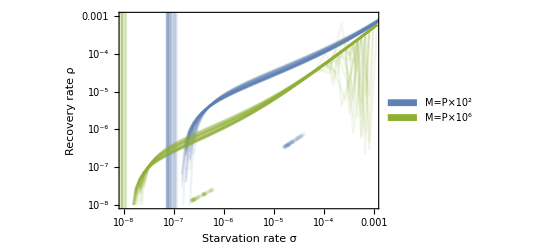

```mathematica
DataHopfPlot=Legended[Show[{
SM,
LM
}],Placed[SwatchLegend[{ColorData[97,1],ColorData[97,3]},{"M=P×10^2","M=P×10^6"},LegendMarkers->"Bubble"],{0.88,0.15}]]
```

```mathematica
Export[StringJoin[{$HomeDirectory,"/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_DataHopf.pdf"}],DataHopfPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/Revision_2017/fig_DataHopf.pdf